Vectors and Matrices as Data

Question 1

```mathematica
Sound@-Graphics-
```

-Graphics-

```mathematica
x=Import["/home/nathan/QEA-Homework/module 2/day3/hornCSV.csv"];
x1=Import["/home/nathan/QEA-Homework/module 2/day3/english_horn.wav","Data"]//Flatten
```

{0.00466919,0.010376,0.00534058,0.00265503,0.0039978,0.00146484,-0.00146484,-0.00311279,38384,-0.00665283,-0.00582886,-0.010498,-0.00796509,-0.00369263,-0.000457764,0.000671387,0.000396729}
 |  |  |  |

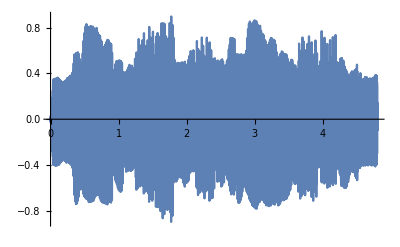

```mathematica
ListLinePlot[x]
```

```mathematica
t=Transpose@Import["/home/nathan/QEA-Homework/module 2/day3/1998DailyTempBos.csv"];
```

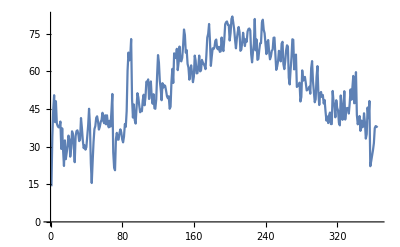

```mathematica
ListLinePlot[t]
```

```mathematica
2.Transpose[x1][[1]]
```

Transpose::nmtx: The first two levels of {0.00466919,0.010376,0.00534058,0.00265503,0.0039978,0.00146484,-0.00146484,-0.00311279,-0.00344849,«33»,0.0155029,0.0135193,0.0136414,0.0169067,0.0230713,0.0341797,0.0192261,0.025116,«38350»} cannot be transposed.

{0.00933838,0.020752,0.0106812,0.00531006,0.00799561,0.00292969,-0.00292969,-0.00622559,-0.00689697,38383,-0.0133057,-0.0116577,-0.0209961,-0.0159302,-0.00738525,-0.000915527,0.00134277,0.000793457}
 |  |  |  |

```mathematica
audio=Sound[SampledSoundList[x1,1500]]
```

-Graphics-

```mathematica
Export["low.flac",audio]
```

low.flac

```mathematica
in=Import["/home/nathan/QEA-Homework/module 2/day3/english_horn.wav","Data"]//Flatten
```

{0.00466919,0.010376,0.00534058,0.00265503,0.0039978,0.00146484,-0.00146484,-0.00311279,38384,-0.00665283,-0.00582886,-0.010498,-0.00796509,-0.00369263,-0.000457764,0.000671387,0.000396729}
 |  |  |  |

Question 2

```mathematica
a={{1}, {2}, {3}};
b={{3}, {2}, {1}};
d={{3, 0, 0}, {0, 2, 0}, {0, 0, 1}};
```

```mathematica
b*a
```

{{3},{4},{3}}

```mathematica
a.b
```

Dot::dotsh: Tensors {{1},{2},{3}} and {{3},{2},{1}} have incompatible shapes.

{{1},{2},{3}}.{{3},{2},{1}}

```mathematica
a.Transpose[b]
```

{{3,2,1},{6,4,2},{9,6,3}}

```mathematica
d.a
```

{{3},{4},{3}}

```mathematica
d.a.Transpose[a]
```

{{3,6,9},{4,8,12},{3,6,9}}

Question 3, 4

```mathematica
Clear["Global`*"]
```

```mathematica
d=Join[
{Join[{1},Table[0,364]]},
Table[Join[Table[0,i-1],{1/3,1/3,1/3},Table[0,363-i]],{i,363}],{Join[Table[0,364],{1}]}
]
```

{1}
 |  |  |  |

```mathematica
t=Import["/home/nathan/QEA-Homework/module 2/day3/1998DailyTempBos.csv"];
```

```mathematica
Dimensions[t]
Dimensions[d]
```

{365,1}

{365,365}

-Graphics-

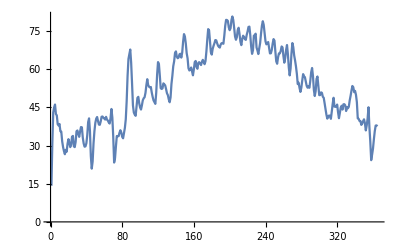

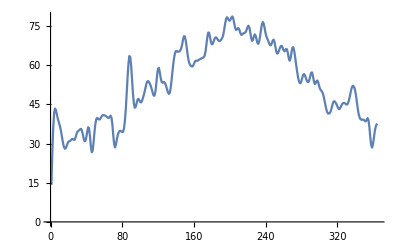

```mathematica
ListLinePlot[Transpose[t]]
ListLinePlot[Transpose[d.t]]
ListLinePlot[Transpose[d.(d.(d.(d.t)))]]
```

Question 7, 8

```mathematica
Clear["Global`*"]
```

```mathematica
soundData=Import["/home/nathan/QEA-Homework/module 2/day3/english_horn.wav","Data"]//Flatten
```

{0.00466919,0.010376,0.00534058,0.00265503,0.0039978,0.00146484,-0.00146484,-0.00311279,38384,-0.00665283,-0.00582886,-0.010498,-0.00796509,-0.00369263,-0.000457764,0.000671387,0.000396729}
 |  |  |  |

```mathematica
Sound[SampledSoundList[soundData,8000]]
```

-Graphics-

```mathematica
d={{1/3}, {1/3}, {1/3}}
```

{{1/3},{1/3},{1/3}}

```mathematica
soundDatad=ListConvolve[dᵀ[[1]],soundData]
```

{0.00679525,0.00612386,0.0039978,0.00270589,0.0013326,-0.0010376,-0.00267537,38384,-0.0110881,-0.00765991,-0.00809733,-0.00738525,-0.00403849,-0.00115967,0.000203451}
 |  |  |  |

```mathematica
Sound[SampledSoundList[soundDatad,8000]]
```

-Graphics-

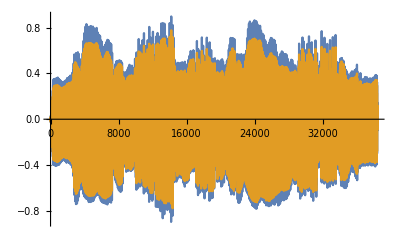

```mathematica
ListLinePlot[{soundData,soundDatad}]
```

Question 9

```mathematica
h={-1,1,0}
```

{-1,1,0}

```mathematica
soundDatah=ListConvolve[h,soundData]
```

{0.0050354,0.00268555,-0.00134277,0.00253296,0.00292969,0.00164795,0.000335693,0.00134277,38382,-0.0141296,-0.000823975,0.00466919,-0.00253296,-0.00427246,-0.00323486,-0.00112915,0.000274658}
 |  |  |  |

```mathematica
Sound[SampledSoundList[soundDatah,8000]]
```

-Graphics-

```mathematica
xhf=Table[Cos[1000t],{t,0,10,10./10000}];
xlf=Table[Cos[10t],{t,0,10,10./10000}];
```

```mathematica
hfSound=ListConvolve[h,xhf];
lfSound=ListConvolve[h,xlf];
```

```mathematica
"High Frequency + High Pass = "Sound[SampledSoundList[hfSound,1000]]
"Low  Frequency + High Pass = " Sound[SampledSoundList[lfSound,1000]]
```

High Frequency + High Pass =  -Graphics-

Low  Frequency + High Pass =  -Graphics-

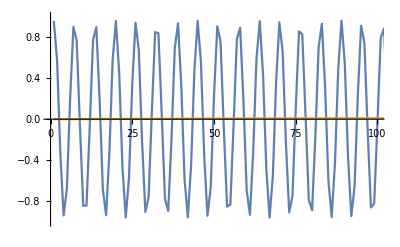

```mathematica
ListLinePlot[{hfSound,lfSound},PlotRange->{{0,100},{-1,1}}]
```

Question 11

{0.00466919,0.010376,0.00534058,0.00265503,0.0039978,0.00146484,-0.00146484,-0.00311279,38384,-0.00665283,-0.00582886,-0.010498,-0.00796509,-0.00369263,-0.000457764,0.000671387,0.000396729}
 |  |  |  |

{1/5,1/5,1/5,1/5,1/5}

{0.00540771,0.00476685,0.00239868,0.000708008,-0.000512695,-0.00227051,-0.00422363,38382,-0.0150452,-0.0136292,-0.0103455,-0.00692749,-0.00568848,-0.00438843,-0.00220947}
 |  |  |  |

High Frequency + High Pass =  -Graphics-

Low  Frequency + High Pass =  -Graphics-

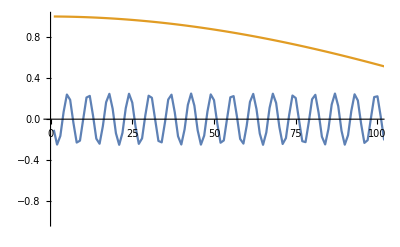

```mathematica
Clear["Global`*"]
soundData=Import["/home/nathan/QEA-Homework/module 2/day3/english_horn.wav","Data"]//Flatten
h2={1/5,1/5,1/5,1/5,1/5}
soundDatah=ListConvolve[h2,soundData]
xhf2=Table[Cos[1000t],{t,0,10,10./10000}];
xlf2=Table[Cos[10t],{t,0,10,10./10000}];
hfSound2=ListConvolve[h2,xhf2];
lfSound2=ListConvolve[h2,xlf2];
"High Frequency + High Pass = "Sound[SampledSoundList[hfSound2,1000]]
"Low  Frequency + High Pass = " Sound[SampledSoundList[lfSound2,1000]]
ListLinePlot[{hfSound2,lfSound2},PlotRange->{{0,100},{-1,1}}]
```

Question 12

```mathematica
Clear["Global`*"]
soundData=Import["/home/nathan/QEA-Homework/module 2/day3/english_horn.wav","Data"]//Flatten
```

{0.00466919,0.010376,0.00534058,0.00265503,0.0039978,0.00146484,-0.00146484,-0.00311279,38384,-0.00665283,-0.00582886,-0.010498,-0.00796509,-0.00369263,-0.000457764,0.000671387,0.000396729}
 |  |  |  |

```mathematica
N@Length[soundData]/8000
```

4.8

```mathematica
h=Join[{1/2},Table[0,8000],{1/2}];
```

```mathematica
soundData[[1;;4000]];
soundData[[Length[soundData]-4000;;Length[soundData]]];
```

```mathematica
SoundDatah=ListConvolve[h,soundData]
soundDatahFull=Join[(1/2)*soundData[[1;;4000]],ListConvolve[h,soundData],(1/2)*soundData[[Length[soundData]-4000;;Length[soundData]]]];
```

{-0.017395,0.0696106,0.087738,-0.00112915,-0.0913849,0.00312805,0.169266,30385,-0.0253754,0.0202484,-0.0189972,-0.0376587,-0.015152,-0.0569,-0.0821228}
 |  |  |  |

```mathematica
Sound[SampledSoundList[soundData,8000]]
Sound[SampledSoundList[SoundDatah,8000]]
Sound[SampledSoundList[soundDatahFull,8000]]
```

-Graphics-

-Graphics-

-Graphics-